# Modelling & Simulations

This is a Wolfram Mathematica Notebook accompanying the report. In this notebook, we will go through the numerical calculations discussed in the report and its preliminary analysis of the results. This notebook will omit the calculations for the Base Model, please refer to the other Wolfram notebook for it. There is also an accompanying Python Notebook, where the calculations used in the report were calculated from. The purpose of this notebook is for the interactive function for users to better understand the plots. For more information please refer to the main report PDF.

## Cure Model (Heaviside Function)

Let us start with defining the default parameters of the system. Here we will assume that the model plays over a short period of time, meaning there is no effects of natural birth and death in play.

```mathematica
(*Define the Cure Model with Heaviside Function*)
cureModel={
S'[t]==Π+γ S[t] HeavisideTheta[t-τ] Z[t]-β S[t] Z[t]-δ,
Z'[t]==β S[t] Z[t]+ζ R[t]-α S[t] Z[t]-γ S[t] Z[t] HeavisideTheta[t-τ],
R'[t]==δ+α S[t] Z[t]-ζ R[t]
};

(*Define Parameters*)
parameters={
α->5/100,(*Zombie Elimination Rate*)
β->53/1000, (*Infection Rate*)
ζ->5/1000, (*Resurrection Rate*)
γ->3/10, (*Cure Effectiveness*)
τ->5, (*Cure Delay*)
δ->0,(*Natural Death Rate of Susceptible -> Assume short timespan*)
Π->0 (*Natural Birth Rate of Susceptible -> Assume short timespan*)
};

(*Define Initial Conditions*)
initialConditions={S[0]==500,Z[0]==1,R[0]==0};

(*Define Time Period*)
timePeriod={t,0,50};
```

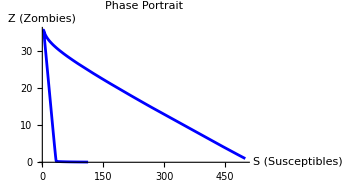

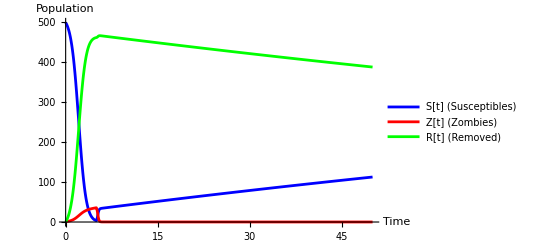

```mathematica
(*Solve the System Numerically*)solution=NDSolve[Join[cureModel/. parameters,initialConditions],{S,Z,R},timePeriod];

(*Phase Portrait:S vs Z*)
phasePortrait=ParametricPlot[Evaluate[{S[t],Z[t]}/. solution],{t,0,50},PlotStyle->Blue,AxesLabel->{"S (Susceptibles)","Z (Zombies)"},PlotLabel->"Phase Portrait",PlotRange->All, AspectRatio->1/2];

(*Time Series Plot for S[t],Z[t],and R[t]*)
timeSeriesPlot=Plot[Evaluate[{S[t],Z[t],R[t]}/. solution],{t,0,50},PlotStyle->{Blue,Red,Green},PlotLegends->{"S[t] (Susceptibles)","Z[t] (Zombies)","R[t] (Removed)"},AxesLabel->{"Time","Population"},PlotRange->All];

(*Display Plots*)
phasePortrait
timeSeriesPlot
```

From this system, we can see that there is an eradication of human. Let the cure effective rate be the main parameter here. Now we know that when the other variables are constant, when gamma = 0.3, human barely got out alive. 

[Note: We will not add user interaction here due to the sheer amount of variables. The addition of a slider crashes the software.]

Knowing that the system is extremely sensitive to starting conditions, let us find the Lyapunov Exponent. In this case, we are going to slightly increase beta to make it more interesting.

*Check python script for *Lyapunov exponent interactive plots*

## Critical Value of Tau

```mathematica
(*Define parameters*)params=<|
"gamma"->0.3,(*Cure effectiveness*)
"beta"->0.053,(*Infection rate*)
"zeta"->0.005,(*Resurrection rate*)
"alpha"->0.05,(*Zombie killing rate*)
"delta"->0.0,(*Susceptible death rate*)
"Pi"->0.0       (*Susceptible birthrate*)
|>;

(*Define the system of differential equations*)
cureModelApprox[t_,y_,tau_,params_]:=Module[{S,Z,R,gamma,beta,zeta,alpha,delta,Pi,Httau,dSdt,dZdt,dRdt},{S,Z,R}=y;
{gamma,beta,zeta,alpha,delta,Pi}=params/@{"gamma","beta","zeta","alpha","delta","Pi"};
Httau=HeavisideTheta[t-tau];(*Heaviside function*)
dSdt=Pi+gamma*S*Httau*Z-beta*S*Z-delta;
dZdt=beta*S*Z+zeta*R-alpha*S*Z-gamma*S*Z*Httau;
dRdt=delta+alpha*S*Z-zeta*R;
{dSdt,dZdt,dRdt}];
```

```mathematica
(*Solve and animate*)Manipulate[Module[{solution,tspan={0,50},y0={100,10,0},sol,S,Z,R,belowThreshold,plot},(*Solve the system of equations*)solution=NDSolveValue[{D[{S[t],Z[t],R[t]},t]==cureModelApprox[t,{S[t],Z[t],R[t]},τ,params],S[0]==100,Z[0]==10,R[0]==0},{S,Z,R},{t,tspan[[1]],tspan[[2]]}];
S=solution[[1]];(*Extract S[t]*)(*Check if S(t) ever falls below 1*)belowThreshold=If[Min[S[t]/. t->Range[0,50,0.1]]<1,"Curve falls below 1 for this value of τ.","Curve stays above 1 for this value of τ."];
(*Create plot*)plot=Plot[S[t],{t,tspan[[1]],tspan[[2]]},PlotStyle->Blue,PlotRange->{{0,50},{0,100}},AxesLabel->{"Time (t)","Susceptible Population (S)"},Epilog->{Red,Dashed,Line[{{0,1},{50,1}}],(*Threshold line*)Text[Style["S = 1 Threshold",Red],{25,5}]},PlotLabel->StringJoin["τ = ",ToString[τ]]];
Column[{plot,Style[belowThreshold,Bold,14]}]],{τ,5,6} (*Animation range for τ*)]
```